# -Graphics-

# Time Series

## Modelling and forecasting

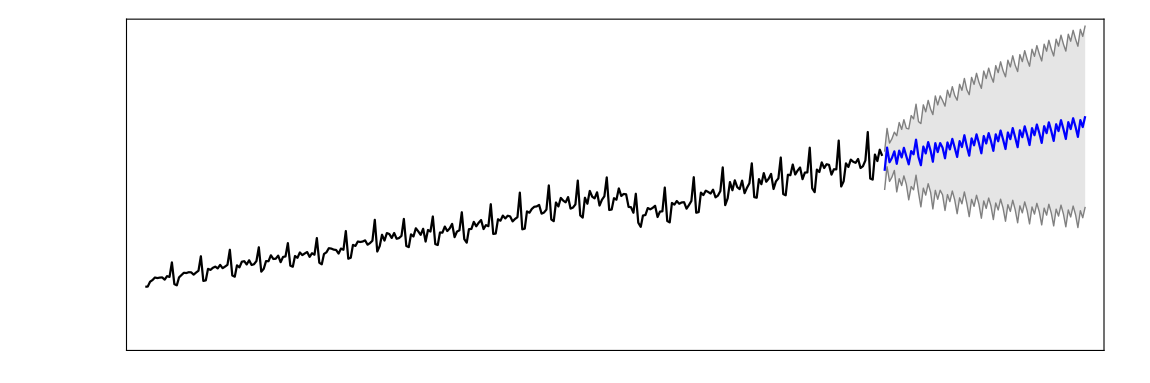

## Outline

### Time Series Processes

Definition of a random process

Random processes in the Wolfram Language

Discrete time, discrete state

Discrete time, continuous state

Continuous time, discrete state

Continuous time, continuous state

Definition of a time series process

Time series processes in the Wolfram Language

MAProcess

SARIMAProcess

ARCHProcess

### Time Series Modelling

Process estimation

Automated model fitting

Manual model fitting

### Time Series Forecasting

Forecasting

Prediction limits

Simulations

## Time Series Processes

Time series processes are are frequently used in fields such as economics, finance, engineering, physics and biology. The Wolfram Language provides a full suite of time series process functionality, including standard process models such as MA, AR and ARMA, as well as several extensions. Models of time series processes can be simulated, estimated from data and used to produce forecasts of future behaviour.

### Random Processes

#### Definition

A random process is a process that evolves stochastically over time, rather than deterministically. Despite its random evolution, steps in a random process that are close in time are dependent, enabling its behaviour to be modelled, simulated and predicted.

Guide: Random Processes.

#### Types of process

Random processes can be discrete or continuous in time and discrete or continuous in state.

### Random Processes in the Wolfram Language

RandomFunction can be used to generate one or more pseudorandom paths of a random process for a specified number of steps.

#### Discrete-time, discrete-state processes

Simulate a random walk on a 2D lattice with RandomWalkProcess:

```mathematica
randomWalk=RandomFunction[RandomWalkProcess[0.5],{0,10^3},2];

ListLinePlot[Transpose[randomWalk["States"]], ]
```

#### Discrete-time, continuous-state processes

Simulate an autoregressive time series process (more on these later):

```mathematica
arProcess = RandomFunction[ARProcess[{0.7},1],{0,50}];

ListPlot[arProcess, ]
```

#### Continuous-time, discrete-state processes

Particles are emitted by a radioactive source according to a Poisson process at the rate of Log[5] per hour. Visualise the number of emitted particles over time:

```mathematica
poissonProcess = RandomFunction[PoissonProcess[Log[5]],{0,10}];

ListLinePlot[poissonProcess, ]
```

#### Continuous-time, continuous-state processes

Simulate Brownian motion in two dimensions:

```mathematica
brownianMotion=RandomFunction[WienerProcess[],{0,1,.001},2];

ListLinePlot[Transpose[brownianMotion["States"]], ]
```

### Time Series Processes

#### Definition

A time series process is a time-stamped random process that is discrete in time and continuous in state.

Guide: Time Series Processes.

#### Types of process

Time series processes in the Wolfram Language are broadly categorised into three areas:

```mathematica
Grid[
{
{Style["Process type", Bold], Style["Wolfram Language functions", Bold]},
{"Autoregressive and Moving-Average (ARMA) Processes", "ARProcess, MAProcess, ARMAProcess"},
{"Integrated and Seasonal ARMA Processes", "ARIMAProcess, SARIMAProcess, SARMAProcess, FARIMAProcess"},
{"Autoregressive Conditional Heteroscedasticity (ARCH) Processes", "ARCHProcess, GARCHProcess"}
},
Alignment -> Left,
Background -> {
None,
{
RGBColor[1.,1.,0.9],
{White, RGBColor[0.8,0.9,0.9]}
}
},
Frame -> All,
Spacings -> {3, 2},
BaseStyle->"Text"
]
```

Process type | Wolfram Language functions
Autoregressive and Moving-Average (ARMA) Processes | ARProcess, MAProcess, ARMAProcess
Integrated and Seasonal ARMA Processes | ARIMAProcess, SARIMAProcess, SARMAProcess, FARIMAProcess
Autoregressive Conditional Heteroscedasticity (ARCH) Processes | ARCHProcess, GARCHProcess

#### Key terms

Autoregressive — data values depend linearly on previous values and on a stochastic term (i.e. the variable is regressed on its own “lagged” values).

Moving average — data values depend linearly on the current and some past values of a stochastic term.

Stationary — the distribution of the data does not change over time.

Weakly stationary — the mean and autocovariance do not change over time and the variance is always finite (i.e. a less strict version of stationarity).

Integrated — each data value has been replaced with the difference between it and the previous value (perhaps multiple times).

Seasonal (data) — data that contains periodic fluctuations (not necessarily related to the weather seasons!).

(Un)conditionally heteroscedastic — variable noise dispersion in data that is (un)conditional on prior dispersion. (No variability would be described as homoscedastic).

### Time Series Processes in the Wolfram Language

#### ARProcess (autoregressive)

ARProcess represents an autoregressive process with the AR coefficients specified. It can be defined in univariate as well as multivariate cases.

Simulate an AR process

```mathematica
arProcess = RandomFunction[ARProcess[{0.5,0.1,0.3,-0.2},1],{0,100}];

ListPlot[arProcess, Filling->Axis]
```

#### MAProcess (moving average)

MAProcess represents a moving-average process with the MA coefficients specified. It can be defined in univariate as well as multivariate cases.

Simulate an MA process:

```mathematica
maProcess = RandomFunction[MAProcess[{0.4,0.3,0.5,0.6},1],{0,100}];

ListPlot[maProcess, Filling->Axis]
```

#### SARIMAProcess (seasonal, autoregressive, integrated, moving average)

SARIMAProcess represents a seasonal integrated autoregressive moving-average process with ARIMA coefficients, seasonal order and seasonal ARIMA coefficients specified. It is effectively the composition of an ARIMA process and a seasonal version of an ARIMA process. It can be generalised to a multivariate case.

Simulate a SARIMA process:

```mathematica
sarimaProcess = RandomFunction[SARIMAProcess[0,{0.4},0,{0.3},{4,{},1,{}},1,{100}], {50}];

ListPlot[sarimaProcess,Filling->Axis]
```

#### ARCHProcess (autoregressive, conditionally heteroscedastic)

ARCHProcess represents an autoregressive conditionally heteroscedastic process.

Simulate an ARCH process:

```mathematica
archProcess = RandomFunction[ARCHProcess[1,{0.3,0.2}],{100}];

ListPlot[archProcess, Filling->Axis]
```

## Time Series Modelling

### Process Estimation

If you know some of the properties of your data (e.g. perhaps you know that it is seasonal), you can estimate the parameters of a suitable random process to model it with EstimatedProcess. The method used by EstimatedProcess to find these parameters can be left to automation or manually customised.

#### Default estimation method

Get S&P 500 data from 2017 using FinancialData and resample it with TimeSeriesResample to ensure that it is regular:

```mathematica
sp500Data=TimeSeriesResample[TimeSeries[FinancialData["SP500",{"2017"}]],"BusinessDay"];

DateListPlot[sp500Data]
```

Suppose you know that the data has the properties of a GeometricBrownianMotionProcess. Find a GBM random process with parameters similar to the data:

```mathematica
estimatedGBMProcess=EstimatedProcess[sp500Data["Values"],GeometricBrownianMotionProcess[a,b,c]]
```

Note that the process has been estimated from the values of the TimeSeries data.

Use the fitted process to simulate 30 similar paths:

```mathematica
gbmPaths=RandomFunction[estimatedGBMProcess,{1,sp500Data["PathLength"],1},30]
```

Add time stamps to the paths:

```mathematica
gbmTimeSeriesPaths=TemporalData[gbmPaths["ValueList"],{sp500Data["FirstDate"],Automatic,"BusinessDay"}]
```

Note that as there are multiple paths, TemporalData has been used instead of TimeSeries.

Compare the simulated paths with the original data:

```mathematica
Show[{
DateListPlot[sp500Data, ],
DateListPlot[gbmTimeSeriesPaths,]
}]
```

#### Custom estimation method

The estimation method used in EstimatedProcess can be chosen with ProcessEstimator.

Get stock data for Google from 2015–2017 and regularise it:

```mathematica
googleStocks=TimeSeries[
FinancialData["GOOGL",{{2015,1,1},{2017,8,1}}],
TemporalRegularity->True
]
```

```mathematica
DateListPlot[googleStocks, ]
```

Model the data with an ARMA process using the default estimator method:

```mathematica
eProcDefault=EstimatedProcess[googleStocks,ARMAProcess[{a,b},{p,q},v]]
```

The method used by EstimatedProcess can be set with ProcessEstimator. The general methods "MaximumLikelihood" and "MethodOfMoments" are defined for most parametric processes. Time series processes can also be estimated using "MaximumConditionalLikelihood" and "SpectralEstimator" methods.

Model the data with each of these estimator methods:

```mathematica
{eProcML, eProcMM,eProcMCL,eProcSE}= Map[
EstimatedProcess[googleStocks,ARMAProcess[{a,b},{p,q},v],ProcessEstimator->#]&,
{"MaximumLikelihood", "MethodOfMoments","MaximumConditionalLikelihood","SpectralEstimator"}
]
```

Autocorrelation (a specific form of cross-correlation) is a way of measuring how well a time series matches up with a lagged version of itself. In the Wolfram Language, this is computed with CorrelationFunction.

Compare the correlation function of the data with the correlation functions of each of the models at lags 0 to 50:

```mathematica
MapThread[
ListPlot[
{
CorrelationFunction[googleStocks,{50}],
CorrelationFunction[#1,{50}]
},
PlotLegends->{"Data",#2},
Filling -> Axis
]&,
{
{eProcDefault, eProcML,eProcMM,eProcMCL,eProcSE},
{"Default", "Max. likelihood", "Method of moments", "Max cond. likelihood", "Spectral"}
}
]
```

### Automated Model Fitting

If you know nothing about the properties of your data, you can have a model chosen automatically with TimeSeriesModelFit. It will choose a suitable parametric model based on a specified criterion, with Akaike information criterion (AIC) being the default.

#### Default model selection criterion

Consider the monthly total number of US international airline passengers (in 1000s) from January 1949 to December 1960:

```mathematica
passengers = TimeSeries[…];
```

It would be reasonable to expect this data to be seasonal (e.g. holiday flights every summer) and to show a positive trend (due to population growth and an increase in flight popularity), which together suggest a SARIMA model might be appropriate.

Visualise the data:

```mathematica
DateListPlot[passengers, ]
```

Fit a suitable time series process to model the data:

```mathematica
passengerModel=TimeSeriesModelFit[passengers];
```

Note that this TimeSeriesModel object contains more information than just the model:

```mathematica
passengerModel["Properties"]
```

Extract the model itself:

```mathematica
passengerModel["BestFit"]
```

See the other models that were considered (rated by AIC):

```mathematica
passengerModel["CandidateSelectionTable"]
```

#### Custom model selection criterion

The default model selection criterion used in TimeSeriesModelFit is AIC, but other choices are available, such as finite sample corrected AIC (AICc), Bayesian information criterion (BIC) and Schwartz-Bayes information criterion (SBC).

Use BIC as the selection criterion instead:

```mathematica
passengerModel2=TimeSeriesModelFit[passengers,Method->{Automatic,"SelectionCriterion"->"BIC"}]
```

As expected, the list of candidate models is now ranked by BIC:

```mathematica
passengerModel2["CandidateSelectionTable"]
```

### Manual Model Fitting

Similar to EstimatedProcess, the model obtained with TimeSeriesModelFit can be constrained to a particular family. The difference is that TimeSeriesModelFit outputs a TimeSeriesModel object, while EstimatedProcess outputs just the model itself.

Get data for the monthly accidental deaths in the US from 1973 to 1978:

```mathematica
accidentalDeathData=TimeSeries[ExampleData[{"Statistics","USAccidentalDeaths"}],{1}];

DateListPlot[TimeSeriesRescale[accidentalDeathData,{"Jan 1973","Dec 1978"}]]
```

Fit a model using the default settings of TimeSeriesModelFit. This gives a SARIMA model with 6th-order seasonality:

```mathematica
deathTimeSeriesAuto=TimeSeriesModelFit[accidentalDeathData]
```

Fit an ARIMA model instead:

```mathematica
deathTimeSeriesARIMA=TimeSeriesModelFit[accidentalDeathData,"ARIMA"]
```

A TimeSeriesModel object has many tests built in to help judge the most suitable fit:

```mathematica
Map[
{#1, deathTimeSeriesARIMA[#1, "LongDescription"]}&,
deathTimeSeriesARIMA["Properties"]
]//TextGrid
```

Plot the autocorrelation function, partial autocorrelation and Ljung–Box plot for the ARIMA model:

```mathematica
Table[
Show[deathTimeSeriesARIMA[plot,"LagMax"->16],ImageSize->175],
{plot,{"ACFPlot","PACFPlot","LjungBoxPlot"}}
]
```

These suggest there is a correlation at lag 12. Fit a SARMA model with 12th-order seasonality:

```mathematica
deathTimeSeriesSARMA=TimeSeriesModelFit[accidentalDeathData,{"SARMA",12}]
```

Compare the original SARIMA model with the new SARMA model by extracting values from various model selection criteria:

```mathematica
With[
{
criteria = {"AIC","AICc","BIC","SBC"}
},
TableForm[
Transpose[
Map[
Function[x, x[criteria]],
{deathTimeSeriesAuto,deathTimeSeriesSARMA}
]
],
TableHeadings->{criteria,{Subscript["SARIMA",6],Subscript["SARMA",12]}}
]
]
```

(Smaller values indicate a better fit.)

Perform an autocorrelation test with AutocorrelationTest:

```mathematica
autoCorrTest = AutocorrelationTest[deathTimeSeriesSARMA["FitResiduals"],12,"HypothesisTestData"]
```

```mathematica
autoCorrTest["TestDataTable"]
autoCorrTest["TestConclusion"]
```

### Exercise 3

In this exercise, you will fit a model to some time series data and verify that it is a good fit.

a) Use TimeSeriesModelFit to fit a model to the TimeSeries data you obtained in Exercise 1.
b) Visualise the correlation and partial correlation to confirm that it is a good fit.

## Time Series Forecasting

### Forecasting

Once a time series model has been fitted to some data, you can use it to make a forecast. This can be done with TimeSeriesForecast.

Recall the airline passenger model seen earlier:

```mathematica
passengers = TimeSeries[…];
passengerModel=TimeSeriesModelFit[passengers];
```

Create a forecast that estimates the number of monthly passengers 5 years into the future:

```mathematica
passengerForecast=TimeSeriesForecast[passengerModel, {5*12}]
```

Visualise the forecast with the original data:

```mathematica
DateListPlot[{passengers, passengerForecast}, ]
```

### Prediction Limits

Rather than computing a single forecast, it can be useful to see upper and lower confidence bands.

##### Automatic prediction limits

This can be done automatically with the "PredictionLimits" property of TimeSeriesModel.

Compute confidence bands at a 95% confidence level:

```mathematica
passengerForecastBounds = TimeSeries[
Map[passengerModel["PredictionLimits", ConfidenceLevel->0.95], passengerForecast["Dates"]],
{"Jan 1st 1961", "Dec 1st 1965"}
]
```

Visualise the bands:

```mathematica
DateListPlot[{passengers, passengerForecast, passengerForecastBounds},]
```

##### Manual prediction limits

Alternatively, you could compute confidence bands manually:

```mathematica
α=0.95;
q=Quantile[NormalDistribution[],1-(1-α)/2];
errors=Sqrt[passengerForecast["MeanSquaredErrors"]];

passengerForecastBounds=TimeSeriesThread[{{1,-q}.#,{1,q}.#}&,{passengerForecast,errors}]
```

Visualise the bands:

```mathematica
DateListPlot[{passengers, passengerForecast, passengerForecastBounds},]
```

### Simulations

Another alternative to taking a single forecast is to simulate many forecasts, then take an average.

Use RandomFunction to simulate 100 forecasts:

```mathematica
simulatedForecasts = RandomFunction[passengerModel,{0,5*12},100];
```

Calculate the mean path:

```mathematica
meanForecast=TimeSeriesThread[Mean,simulatedForecasts];
```

Visualise all of the simulated paths:

```mathematica
DateListPlot[{passengers, simulatedForecasts, meanForecast}, ]
```

### Exercise 4

In this exercise, you will take a model fitted to some data and obtain a forecast.

a) Use TimeSeriesForecast to obtain a forecast 25 time stamps into the future for the model you created in Exercise 3.
b) Extract the errors from your forecast (hint: use "MeanSquaredErrors").
c) Use TimeSeriesThread to get upper and lower limits for your forecast.
d) Plot the fit and the data, along with the limits.

## Summary

There are four types of random process in the Wolfram Language (discrete time and discrete state; discrete time and continuous state; continuous time and discrete state; continuous time and continuous state).

There are three broad categories of time series process in the Wolfram Language (AR and MA processes; integrated and seasonal ARMA processes; ARCH processes).

Time series processes can be fitted to data (manually or automatically) and used to model/simulate new data.

Time series models can be used to forecast/extrapolate (with prediction limits).